```mathematica
Shifted[λ_,n_]:=Module[{padded},padded=PadRight[λ,n];Map[padded⟦#⟧+Max[n-#,0]&,Range[Length[padded]]]]
VandermondeDet[x_]:=Apply[Times,Flatten[Table[If[i<j,x⟦i⟧-x⟦j⟧,1],{i,1,Length[x]},{j,1,Length[x]}]]]
```

```mathematica
Frob[λ_,n_]:=Factorial[Total[λ]]/Apply[Times,Map[Factorial,Shifted[λ,n]]]*VandermondeDet[Shifted[λ,n]]
```

```mathematica
λ={5,4,2,1};
```

```mathematica
Map[Shifted[λ,#]&,Range[Length[λ],15]]
```

{{8,6,3,1},{9,7,4,2,0},{10,8,5,3,1,0},{11,9,6,4,2,1,0},{12,10,7,5,3,2,1,0},{13,11,8,6,4,3,2,1,0},{14,12,9,7,5,4,3,2,1,0},{15,13,10,8,6,5,4,3,2,1,0},{16,14,11,9,7,6,5,4,3,2,1,0},{17,15,12,10,8,7,6,5,4,3,2,1,0},{18,16,13,11,9,8,7,6,5,4,3,2,1,0},{19,17,14,12,10,9,8,7,6,5,4,3,2,1,0}}

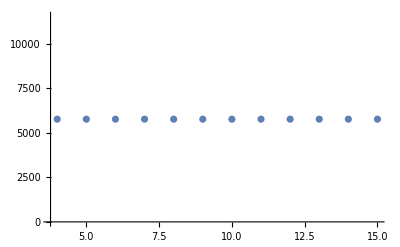

```mathematica
ListPlot[Map[{#,Frob[λ,#]}&,Range[Length[λ],15]]]
```